{}

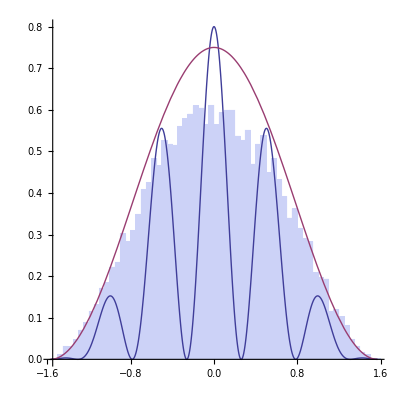
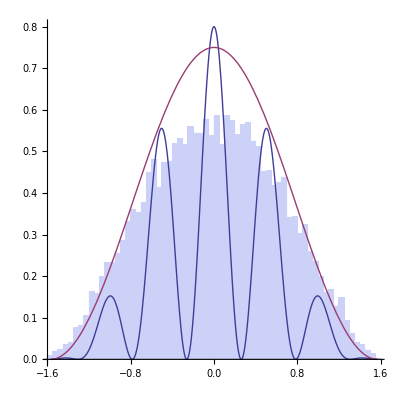
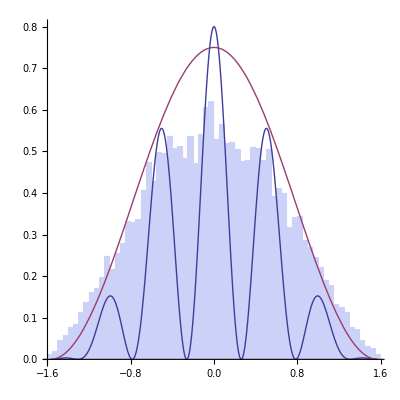
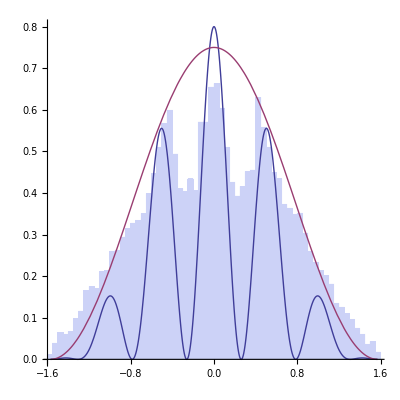
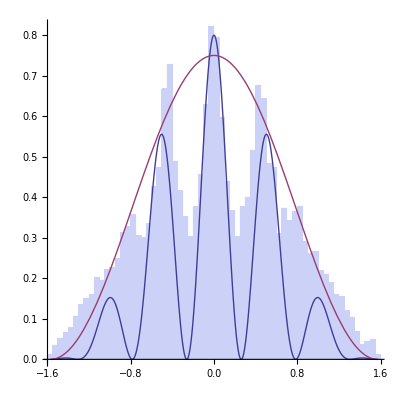
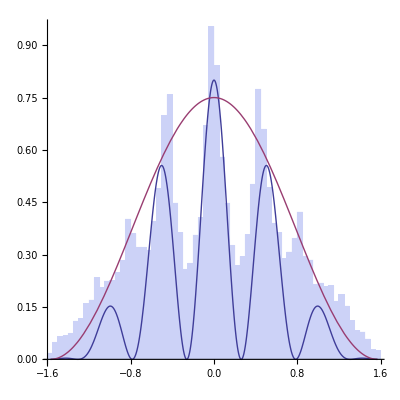
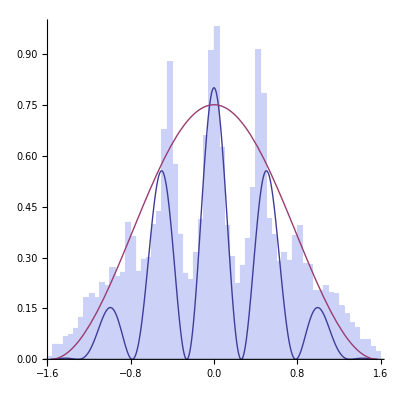
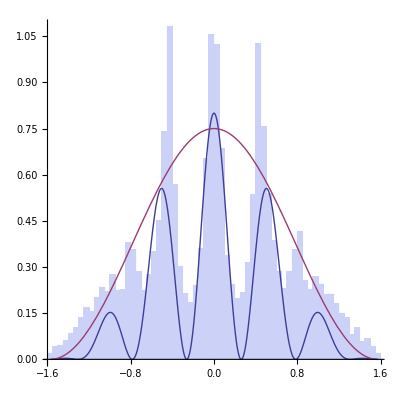
{-Graphics-1,-Graphics-2.5,-Graphics-5,-Graphics-7.5,-Graphics-10,-Graphics-12.5,-Graphics-15,-Graphics-20,-Graphics-30,-Graphics-40}

```mathematica
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
yoyoyo = {}
Do[
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAutoM"<> ToString[MEMVALUE]<>".dat"]];
AppendTo[yoyoyo,Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[{0.8Sinc[2x]^2 Cos[6x]^2,1.5Cos[x]^2/2},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[MEMVALUE],{{Right,Top}}]],
{MEMVALUE,MEMORYLIST}]
yoyoyo
```

{}

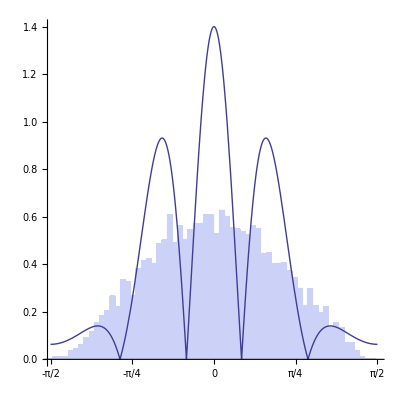
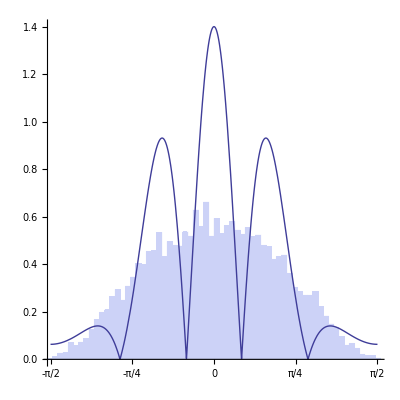
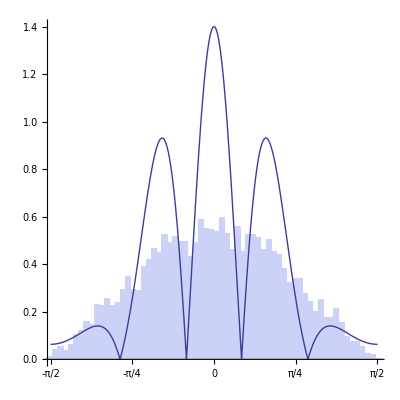
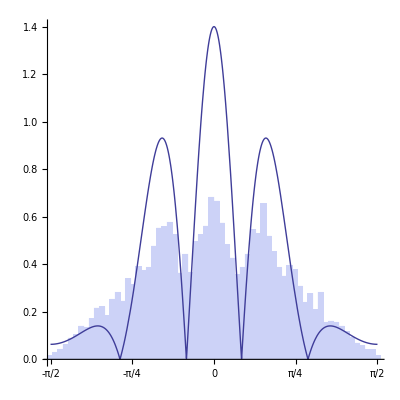
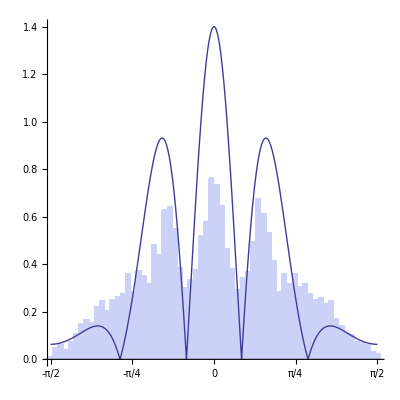
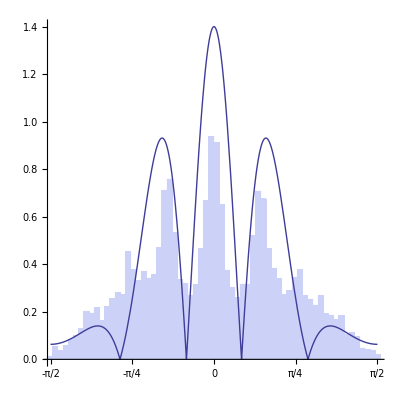
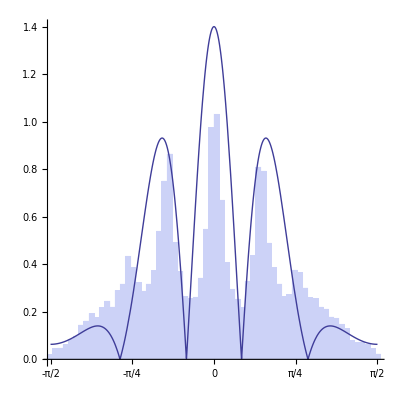
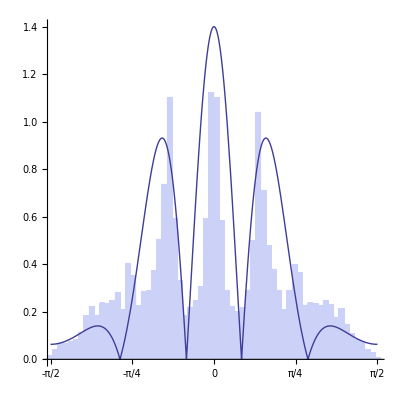
{-Graphics-1,-Graphics-2.5,-Graphics-5,-Graphics-7.5,-Graphics-10,-Graphics-12.5,-Graphics-15,-Graphics-20,-Graphics-30,-Graphics-40}

```mathematica
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
yoyoyo = {}
Do[
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M"<> ToString[MEMVALUE]<>".dat"]];
AppendTo[yoyoyo,Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}],Plot[{1.4(Abs[Sinc[3Sin[x]] Cos[6Sin[x]]])},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[MEMVALUE],{{Right,Top}}]],
{MEMVALUE,MEMORYLIST}]
yoyoyo
```

{}

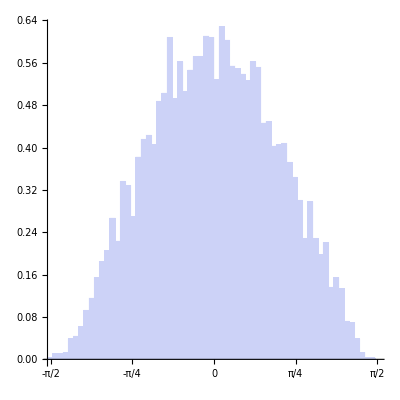
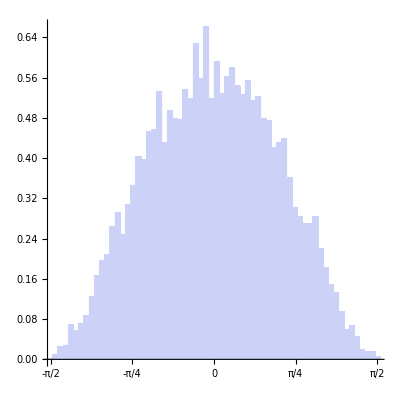
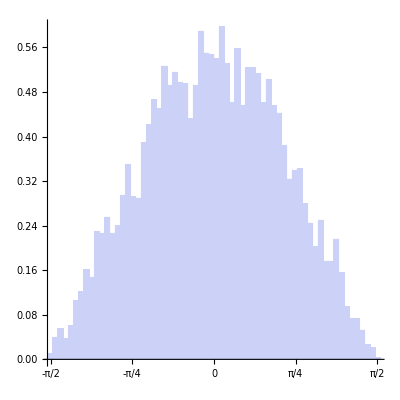
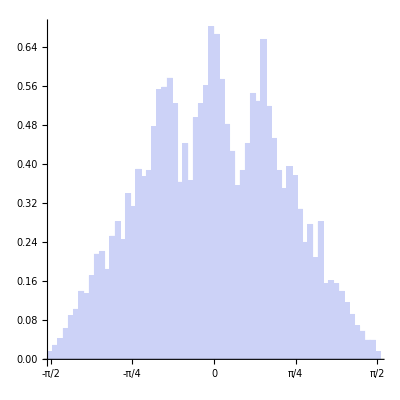
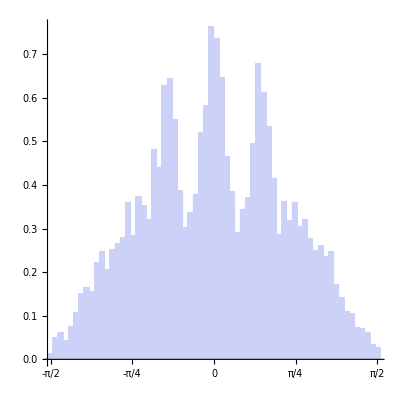
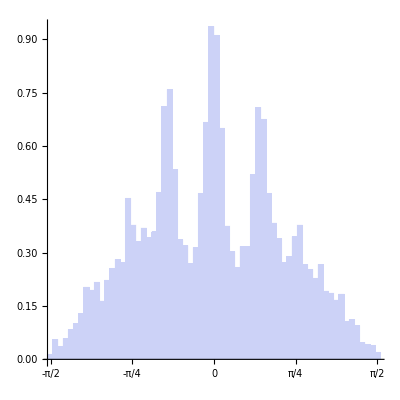
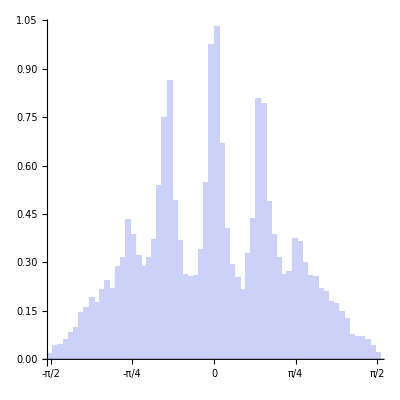
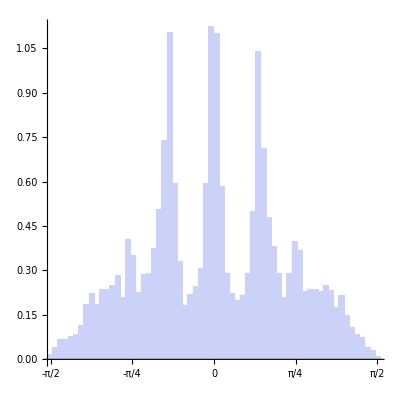
{-Graphics-1,-Graphics-2.5,-Graphics-5,-Graphics-7.5,-Graphics-10,-Graphics-12.5,-Graphics-15,-Graphics-20,-Graphics-30,-Graphics-40}

```mathematica
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
yoyoyo = {}
Do[
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M"<> ToString[MEMVALUE]<>".dat"]];
AppendTo[yoyoyo,Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}]}],ToString[MEMVALUE],{{Right,Top}}]],
{MEMVALUE,MEMORYLIST}]
yoyoyo
```

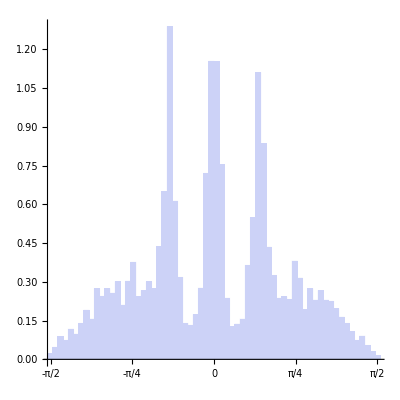

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M40.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}]}]
```

```mathematica
ExpToTrig[ⅇ^(ⅈ (k)^2 t+ⅈ k x) Cos[d k] Sin[(k w)/2]/k]
```

(Cos[d k] Cos[k^2 t+k x] Sin[(k w)/2])/k+(ⅈ Cos[d k] Sin[(k w)/2] Sin[k^2 t+k x])/k

```mathematica
Cos[k^2 t+k x]Cos[d k] Sin[(k w)/2]/k
```

(Cos[d k] Cos[k^2 t+k x] Sin[(k w)/2])/k

```mathematica
((Cos[d k-k^2 t-k x]+Cos[d k+k^2 t+k x])/2  Sin[(k w)/2])/k
```

((Cos[d k-k^2 t-k x]+Cos[d k+k^2 t+k x]) Sin[(k w)/2])/(2 k)

```mathematica
(Cos[d k-k^2 t-k x] Sin[(k w)/2])/(2 k)
```

(Cos[d k-k^2 t-k x] Sin[(k w)/2])/(2 k)

```mathematica
((Sin[d k-k^2 t-k x+(k w)/2] -Sin[d k-k^2 t-k x-(k w)/2])/2)/(2 k)
```

(-Sin[d k-k^2 t-(k w)/2-k x]+Sin[d k-k^2 t+(k w)/2-k x])/(4 k)

```mathematica
FullSimplify[Sin[d k-k^2 t+(k w)/2-k x]/(4 k)]
```

Sin[1/2 k (2 d-2 k t+w-2 x)]/(4 k)

```mathematica
Integrate[Sin[1/2 k (2 d-2 k t+w-2 x)]/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

(π √t (Abs[t] FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+t FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)]))/(4 Abs[t]^(3/2))

```mathematica
FullSimplify[(π √t (t FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+t FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)]))/(4 t^(3/2))]
```

1/4 π (FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)])

```mathematica
Integrate[(-Sin[d k-k^2 t-(k w)/2-k x])/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

(π √t (Abs[t] FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+t FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)]))/(4 Abs[t]^(3/2))

```mathematica
FullSimplify[(π √t (t FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+t FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)]))/(4 t^(3/2))]
```

1/4 π (FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)])

```mathematica
FullSimplify[1/4 π (FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)])+1/4 π (FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)])]
```

1/4 π (FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)])

```mathematica
((Cos[d k+k^2 t+k x]) Sin[(k w)/2])/(2 k)
```

(Cos[d k+k^2 t+k x] Sin[(k w)/2])/(2 k)

```mathematica
((Sin[d k+k^2 t+k x+(k w)/2] -Sin[d k+k^2 t+k x-(k w)/2])/2)/(2 k)
```

```mathematica
(-Sin[d k+k^2 t-(k w)/2+k x]+Sin[d k+k^2 t+(k w)/2+k x])/(4 k)
```

```mathematica
Integrate[(-Sin[d k+k^2 t-(k w)/2+k x])/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

(π √t (Abs[t] FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+t FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]))/(4 Abs[t]^(3/2))

```mathematica
Integrate[Sin[d k+k^2 t+(k w)/2+k x]/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

1/(5160960 t^2 Abs[t]^(3/2))√(π/2) (2 d+w+2 x) (1008 Abs[t] (640 t^2 Cos[(2 d+w+2 x)^2/(16 t)]+(2 d+w+2 x)^4 HypergeometricPFQ[{5/4},{3/2,9/4},-(2 d+w+2 x)^4/(1024 t^2)])+5 ((2 d+w+2 x)^6 HypergeometricPFQ[{7/4},{5/2,11/4},-(2 d+w+2 x)^4/(1024 t^2)]+43008 t^3 Sin[(2 d+w+2 x)^2/(16 t)]))

```mathematica
FullSimplify[(π √t (t FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+t FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)]))/(4 t^(3/2))]
```

1/4 π (FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)])

```mathematica
FullSimplify[(π √t (t FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+t FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]))/(4 t^(3/2))]
FullSimplify[1/4 π (FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)])]
```

1/4 π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)])

1/4 π (FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)])

```mathematica
FullSimplify[1/4 π (FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)])+(1/4 π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]))+(1/4 π (FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)]))]
```

1/4 π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelC[(2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(-2 d+w+2 x)/(2 √(2 π) √t)]+FresnelS[(2 d+w+2 x)/(2 √(2 π) √t)])

```mathematica
(ⅈ Cos[d k] Sin[(k w)/2] Sin[k^2 t+k x])/k
```

(ⅈ Cos[d k] Sin[(k w)/2] Sin[k^2 t+k x])/k

```mathematica
(ⅈ Cos[d k] (Cos[(k w)/2-k^2 t-k x] -Cos[(k w)/2+k^2 t+k x])/2)/k
```

(ⅈ Cos[d k] (Cos[k^2 t-(k w)/2+k x]-Cos[k^2 t+(k w)/2+k x]))/(2 k)

```mathematica
(ⅈ( (Cos[d k-(k^2 t-(k w)/2+k x)]+Cos[d k+(k^2 t-(k w)/2+k x)])-(Cos[d k-(k^2 t+(k w)/2+k x)] +Cos[d k+(k^2 t+(k w)/2+k x)]))/2)/(2 k)
```

(ⅈ (-Cos[d k-k^2 t-(k w)/2-k x]+Cos[d k-k^2 t+(k w)/2-k x]+Cos[d k+k^2 t-(k w)/2+k x]-Cos[d k+k^2 t+(k w)/2+k x]))/(4 k)

```mathematica
Integrate[(ⅈ Cos[d k] Sin[(k w)/2] Sin[k^2 t+k x])/k,{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

$Aborted

```mathematica
Integrate[ⅈ Cos[d k] Sin[(k w)/2] Sinc[k^2 t+k x],{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

$Aborted

```mathematica
Integrate[(-Cos[d k-k^2 t-(k w)/2-k x])/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

Integrate[Cos[d k+k^2 t-(k w)/2-k x]/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]

```mathematica
Integrate[(ⅈ (Cos[d k-k^2 t+(k w)/2-k x]))/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

$Aborted

```mathematica
Integrate[(ⅈ (Cos[d k+k^2 t-(k w)/2+k x]))/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

```mathematica
Integrate[(ⅈ (-Cos[d k+k^2 t+(k w)/2+k x]))/(4 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

```mathematica
TrigToExp[(ⅈ (Cos[d k-k^2 t+(k w)/2-k x]))/(4 k)]
```

(ⅈ ⅇ^(ⅈ d k-ⅈ k^2 t+(ⅈ k w)/2-ⅈ k x))/(8 k)+(ⅈ ⅇ^(-ⅈ d k+ⅈ k^2 t-(ⅈ k w)/2+ⅈ k x))/(8 k)

```mathematica
Integrate[(ⅈ ⅇ^(-ⅈ d k+ⅈ k^2 t-(ⅈ k w)/2+ⅈ k x))/(8 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]
```

Integrate::idiv: Integral of ⅇ^-1/2\ ⅈ\ k\ (2\ d + w - 2\ (k\ t + x))/k does not converge on {-∞, ∞}.

Integrate[(ⅈ ⅇ^(-ⅈ d k+ⅈ k^2 t-(ⅈ k w)/2+ⅈ k x))/(8 k),{k,-∞,∞},Assumptions:>t∈Reals&&d∈Reals&&w∈Reals&&x∈Reals]

```mathematica
cheddar[x_,d_]:=(1/d(1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))
```

```mathematica
FullSimplify[(cheddar[x-d,w/2]+cheddar[x+d,w/2])/2]
```

1/w(1/2+ⅈ/2) π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)]))

```mathematica
FullSimplify[(1/w(1/2+ⅈ/2) π)(1/w(1/2-ⅈ/2) π)]
```

π^2/(2 w^2)

```mathematica
Simplify[π^2/(2 w^2)((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])))*((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]+ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])))]
```

1/(2 w^2)π^2 (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])) (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]+ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)]))

```mathematica
poopGouda[x_,t_,d_,w_]:=1/w(1/2+ⅈ/2) π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)]))
poopGoudaCo[x_,t_,d_,w_]:=1/w(1/2-ⅈ/2) π (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]+ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)]))
```

```mathematica
FullSimplify[(x-ⅈ y)(x+ⅈ y)]
```

x^2+y^2

```mathematica
FullSimplify[π^2/(2 w^2)(((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2))]
```

1/(2 w^2)π^2 ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2)

```mathematica
poopCheddar[x_,t_,d_,w_]:=1/(2 w^2)π^2 ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2)
```

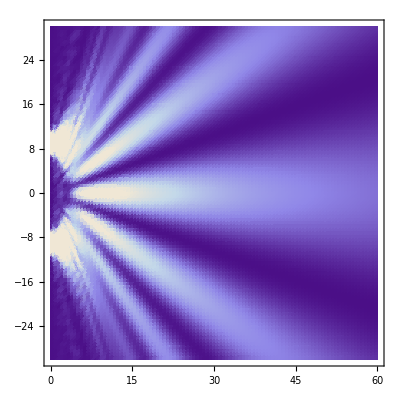

```mathematica
DensityPlot[poopCheddar[y,x,9,4],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

```mathematica
(poopGoudaCo[x,t,d,w]D[poopGouda[x,t,d,w],x]-poopGouda[x,t,d,w]D[poopGoudaCo[x,t,d,w],x])/poopCheddar[x,t,d,w]
```

(2 w^2 (1/(2 w^2)π^2 (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]+ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])) (-Cos[(-2 d+w-2 x)^2/(16 t)]/(√(2 π) √t)-Cos[(d+w/2-x)^2/(4 t)]/(√(2 π) √t)+Cos[(-d+w/2+x)^2/(4 t)]/(√(2 π) √t)+Cos[(d+w/2+x)^2/(4 t)]/(√(2 π) √t)-ⅈ (-Sin[(-2 d+w-2 x)^2/(16 t)]/(√(2 π) √t)-Sin[(d+w/2-x)^2/(4 t)]/(√(2 π) √t)+Sin[(-d+w/2+x)^2/(4 t)]/(√(2 π) √t)+Sin[(d+w/2+x)^2/(4 t)]/(√(2 π) √t)))-1/(2 w^2)π^2 (FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])) (-Cos[(-2 d+w-2 x)^2/(16 t)]/(√(2 π) √t)-Cos[(d+w/2-x)^2/(4 t)]/(√(2 π) √t)+Cos[(-d+w/2+x)^2/(4 t)]/(√(2 π) √t)+Cos[(d+w/2+x)^2/(4 t)]/(√(2 π) √t)+ⅈ (-Sin[(-2 d+w-2 x)^2/(16 t)]/(√(2 π) √t)-Sin[(d+w/2-x)^2/(4 t)]/(√(2 π) √t)+Sin[(-d+w/2+x)^2/(4 t)]/(√(2 π) √t)+Sin[(d+w/2+x)^2/(4 t)]/(√(2 π) √t)))))/(π^2 ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2))

```mathematica
Simplify[(poopGoudaCo[x,t,d,w]D[poopGouda[x,t,d,w],x]-poopGouda[x,t,d,w]D[poopGoudaCo[x,t,d,w],x])]
```

1/(2 √2 √t w^2)π^(3/2) ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]-ⅈ FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]-ⅈ FresnelS[(d+w/2-x)/(√(2 π) √t)]-ⅈ FresnelS[(-d+w/2+x)/(√(2 π) √t)]-ⅈ FresnelS[(d+w/2+x)/(√(2 π) √t)]) (Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]+ⅈ Sin[(-2 d+w-2 x)^2/(16 t)]+ⅈ Sin[(2 d+w-2 x)^2/(16 t)]-ⅈ Sin[(d+w/2+x)^2/(4 t)]-ⅈ Sin[(-2 d+w+2 x)^2/(16 t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]+ⅈ FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+ⅈ FresnelS[(d+w/2-x)/(√(2 π) √t)]+ⅈ FresnelS[(-d+w/2+x)/(√(2 π) √t)]+ⅈ FresnelS[(d+w/2+x)/(√(2 π) √t)]) (Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]-ⅈ Sin[(-2 d+w-2 x)^2/(16 t)]-ⅈ Sin[(2 d+w-2 x)^2/(16 t)]+ⅈ Sin[(d+w/2+x)^2/(4 t)]+ⅈ Sin[(-2 d+w+2 x)^2/(16 t)]))

```mathematica
FullSimplify[(poopGoudaCo[x,t,d,w]D[poopGouda[x,t,d,w],x]-poopGouda[x,t,d,w]D[poopGoudaCo[x,t,d,w],x])]
```

-1/(√2 √t w^2)ⅈ π^(3/2) ((Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]) (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]) (Sin[(-2 d+w-2 x)^2/(16 t)]+Sin[(2 d+w-2 x)^2/(16 t)]-Sin[(d+w/2+x)^2/(4 t)]-Sin[(-2 d+w+2 x)^2/(16 t)]))

```mathematica
FullSimplify[(-1/(√2 √t w^2) π^(3/2) ((Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]) (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]) (Sin[(-2 d+w-2 x)^2/(16 t)]+Sin[(2 d+w-2 x)^2/(16 t)]-Sin[(d+w/2+x)^2/(4 t)]-Sin[(-2 d+w+2 x)^2/(16 t)])))/poopCheddar[x,t,d,w]]
```

-(√(2/π) ((Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]) (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]) (Sin[(-2 d+w-2 x)^2/(16 t)]+Sin[(2 d+w-2 x)^2/(16 t)]-Sin[(d+w/2+x)^2/(4 t)]-Sin[(-2 d+w+2 x)^2/(16 t)])))/(√t ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2))

```mathematica
VelocityField5[x_,t_,d_,w_]:=-(√(2/π) ((Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]) (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]) (Sin[(-2 d+w-2 x)^2/(16 t)]+Sin[(2 d+w-2 x)^2/(16 t)]-Sin[(d+w/2+x)^2/(4 t)]-Sin[(-2 d+w+2 x)^2/(16 t)])))/(√t ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2))
```

```mathematica
ddd = 9.0;
σσσ=2.0;
Parallelize[
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField5[y[t], t, ddd,2σσσ ]/1,y[0.1]== ddd+RandomVariate[UniformDistribution[{-σσσ,σσσ}]]},y,{t,0.1,60}],{4*16}];
HollandtablD=
Table[NDSolve[{D[y[t], t]==-VelocityField5[y[t], t, ddd,2σσσ ]/1,y[0.1]== -ddd+RandomVariate[UniformDistribution[{-σσσ,σσσ}]]},y,{t,0.1,60}],{4*16}];
];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0.1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

$Aborted

InterpolatingFunction::dmval: Input value {0.101224} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

ReplaceAll::reps: {HollandtablD} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-